```mathematica
number:=Table[If[x<10,"0"<>ToString[x],ToString[x]],{x,0,99}];classical =Table[File["C:\\Users\\oscar\\OneDrive\\Wolfram\\genres\\classical\\__classical.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
jazz =Table[File["C:\\Users\\oscar\\OneDrive\\Wolfram\\genres\\jazz\\__jazz.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
rock=Table[File["C:\\Users\\oscar\\OneDrive\\Wolfram\\genres\\rock\\__rock.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
hiphop=Table[File["C:\\Users\\oscar\\OneDrive\\Wolfram\\genres\\hiphop\\__hiphop.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
pop = Table[File["C:\\Users\\oscar\\OneDrive\\Wolfram\\genres\\pop\\__pop.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
popTest = Drop[pop,95];
pop = Drop[pop,-5];
classicalTest = Drop[classical,95];
classical = Drop[classical,-5];
rockTest = Drop[rock,95];
rock = Drop[rock,-5];
jazzTest = Drop[jazz,95];
jazz = Drop[jazz,-5];
hiphopTest = Drop[hiphop,95];
hiphop = Drop[hiphop,-5];
```

```mathematica
genres = {"classical","jazz","rock","hiphop","pop"};
musicGenres = Flatten[Table[Table[genres⟦x⟧,95],{x,5}]];
testGenres = Flatten[Table[Table[genres⟦x⟧,5],{x,5}]];
musicTest = Join[classicalTest,jazzTest,rockTest,hiphopTest,popTest];
```

```mathematica
data = RandomSample[Thread[Join[classical,jazz,rock,hiphop,pop]-> musicGenres]];
validation = Thread[musicTest-> testGenres];
```

```mathematica
(*données pour tests*)
```

```mathematica
Clear[rnnNet]
rnnNet = NetInitialize@NetChain[{
GatedRecurrentLayer[400],
SequenceLastLayer[], 
Ramp,
LinearLayer[50],
Ramp,
LinearLayer[5],
SoftmaxLayer[]
},"Input"->NetEncoder["AudioMelSpectrogram"],
"Output"-> NetDecoder[{"Class",genres}]]
```

NetChain[<>]

```mathematica
trained = NetTrain[rnnNet,data,BatchSize -> 2,MaxTrainingRounds->15, TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
measurements = ClassifierMeasurements[trained,validation]
```

ClassifierMeasurementsObject[…]

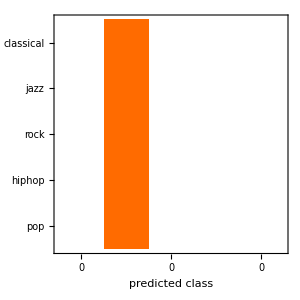

0.2

```mathematica
measurements["ConfusionMatrixPlot"]
measurements["Accuracy"]
```

```mathematica
Clear[audio]
audio = AudioCapture[]
```

```mathematica
trained[audio]
```

classical

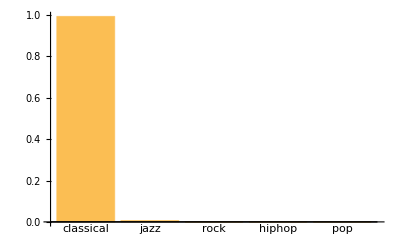

```mathematica
a = Import["C:\\Users\\oscar\\OneDrive\\Documents\\Wolfram\\genres\\classical\\classical.00098.au"]

BarChart[trained[a,"Probabilities"],ChartLabels-> genres]
```